```mathematica
Clear["`*"]
```

Directory:

```mathematica
InputField[Dynamic[GetDirectory],String]
```

File Name:

```mathematica
InputField[Dynamic[filename],String]
```

```mathematica
SetDirectory[GetDirectory];
mydata=ReadList[filename,{Number,Number}];
```

SetDirectory::fstr: File specification GetDirectory is not a string of one or more characters.

Function:
(note: don't use C,D,E,I,K,N or O as parameters)

```mathematica
InputField[Dynamic[function],Expression]
```

Parameters:
(note: must be in list form, i.e. {a,b,c})

```mathematica
InputField[Dynamic[params]]
```

Parameter Values:
(note: must be in list form, i.e. {1,2,3})

```mathematica
InputField[Dynamic[vals]]
```

{a→4.91292,b→15.0691,c→0.0139571,d→-0.0312897}

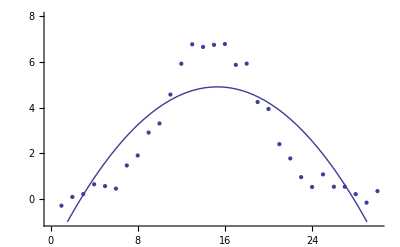

```mathematica
parameters=Transpose[{params,vals}];
BestFit=FindFit[mydata,function,parameters,x]
P2=Plot[(function)/.BestFit,{x,0,30},PlotRange->{{0,30},{-1,8}}];
P1=ListPlot[mydata,PlotRange->{{0,30},{-1,8}}];


Show[P1,P2]
```

```mathematica
paramtable=Table[BestFit[[i,2]],{i,1,Length[params]}];

Setvalue[list_,values_]:=MapThread[Set,{Take[list,Min[Length[list],Length[values]]],Take[values,Min[Length[list],Length[values]]]}];
Setvalue[params,paramtable];
x=Table[mydata[[i,1]],{i,1,Length[mydata]}];
mydatay=Table[mydata[[i,2]],{i,1,Length[mydata]}];
χSquared=Total[(mydatay-function)^2/function];
RedχSqaured=χSquared/(Length[mydata]-Length[params]);
```